```mathematica
w[x_,y_,n_]:=Style[{AbsoluteThickness[2/3],Line[{{x,y},{x,y-.7}}],RGBColor[.8,.8,1],Polygon[{{x-.3,y-.7},{x+.3,y-.7},{x+.4,y-1.3},{x-.4,y-1.3}}],GrayLevel[0],Text[Style[n,FontSize->14],{x,y-1.05}]},Antialiasing->False]
```

```mathematica
w[x_,y_,n_]:=Style[{AbsoluteThickness[2/3],Line[{{x,y},{x,y-.7}}],RGBColor[.8,.8,1],Polygon[{{x-.3,y-.7},{x+.3,y-.7},{x+.4,y-1.3},{x-.4,y-1.3}}]},Antialiasing->False]
```

```mathematica
w[x_,y_,n_]:=Style[{Line[{{x,y},{x,y-.7}}],Line[{{x-.3,y-.7},{x+.3,y-.7},{x+.4,y-1.3},{x-.4,y-1.3},{x-.3,y-.7}}],Text[Style[n,FontFamily->"Courier", FontSize->20],{x,y-1.05}]},Antialiasing->False]
```

```mathematica
w[x_,y_,n_]:=Style[{Line[{{x,y},{x,y-.7}}],Line[{{x-.3,y-.7},{x+.3,y-.7},{x+.4,y-1.3},{x-.4,y-1.3},{x-.3,y-.7}}]},Antialiasing->False]
```

```mathematica
l[x_,y_,n_,m_,p_]:=Style[{AbsoluteThickness[2/3],Line[{{x,y},{x+n,y}}],Table[Line[{{a,y-1/12},{a,y+1/12}}],{a,x,x+n,m}],Line[{{p,y},{p,y+1}}]},Antialiasing->False]
```

```mathematica
ll[x_,y_,n_,m_,p_]:=Style[{Line[{{x,y},{x+n,y}}],Table[Line[{{a,y-1/12},{a,y+1/12}}],{a,x,x+n,m}],Line[{{p,y},{p,y+2}}]},Antialiasing->False]
```

```mathematica
lll[x_,y_,n_,m_,p_]:=Style[{Line[{{x,y},{x+n,y}}],Table[Line[{{a,y-1/12},{a,y+1/12}}],{a,x,x+n,m}],Line[{{p,y},{p,y+4}}]},Antialiasing->False]
```

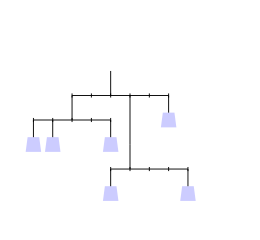

```mathematica
Show[Graphics[{w[0,2,4],w[1,2,2],w[4,2,5],l[0,2,4,1,2],w[4,0,3],w[8,0,1],l[4,0,4,1,5],l[2,3,5,1,4],w[7,3,6],AbsoluteThickness[2/3],Line[{{5,1},{5,3}}]}],AspectRatio->Automatic,PlotRange->{{-0.5,10.5},{-2,6}},ImageSize->{260,240}]
```

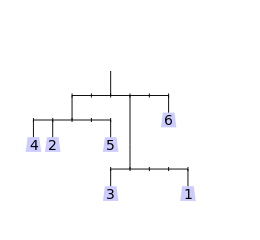

```mathematica
Show[Graphics[{w[0,2,4],w[1,2,2],w[4,2,5],l[0,2,4,1,2],w[4,0,3],w[8,0,1],l[4,0,4,1,5],l[2,3,5,1,4],w[7,3,6],AbsoluteThickness[2/3],Line[{{5,1},{5,3}}]}],AspectRatio->Automatic,PlotRange->{{-0.5,10.5},{-2,6}},ImageSize->{260,240}]
```

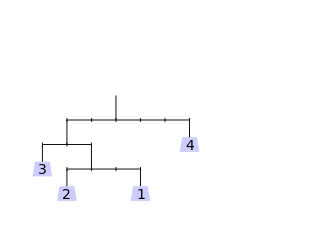

```mathematica
Show[Graphics[{w[1,0,2],w[4,0,1],l[1,0,3,1,2],w[0,1,3],l[0,1,2,1,1],l[1,2,5,1,3],w[6,2,4]}],AspectRatio->Automatic,PlotRange->{{-0.5,10.5},{-2,6}},ImageSize->{330,240}]
```

```mathematica
Show[Graphics[{w[0,0,1],w[1,0,3],w[3,0,5],ll[0,0,3,1,2],w[4,0,4],w[7,0,2],ll[4,0,3,1,5],w[6,2,6],l[2,2,4,1,4]}],AspectRatio->Automatic,PlotRange->{{-0.5,10.5},{-2,6}},ImageSize->{330,240}]
```

```mathematica
Show[Graphics[{w[0,0,7],w[1,0,4],w[5,0,2],w[6,0,3],ll[0,0,6,1,2],w[1,3,6],l[1,3,4,1,3],w[4,2,8],w[6,2,5],w[8,2,1],l[4,2,4,1,5],Line[{{2,2},{2,3}}]}],AspectRatio->Automatic,PlotRange->{{-0.5,10.5},{-2,6}},ImageSize->{330,240}]
```

```mathematica
Show[Graphics[{w[0,2,7],w[2,2,5],w[3,2,1],w[4,2,2],w[5,2,6],w[7,2,10],w[8,2,4],w[11,2,8],l[0,2,3,1,1],l[4,2,3,1,6],l[8,2,3,1,10],w[9,0,3],w[13,0,9],l[9,0,4,1,12],Line[{{12,1},{12,3}}],l[1,3,11,1,7]}],AspectRatio->Automatic,PlotRange->{{-0.5,14.5},{-2,6}},ImageSize->{450,240}]
```

```mathematica
Show[Graphics[{w[0,0,1],w[1,0,2],w[2,0,3],w[4,0,10],w[6,0,5],w[7,0,8],w[10,0,9],w[11,1,11],ll[0,0,4,1,3],l[6,0,4,1,8],w[0,2,6],w[1,2,4],l[0,2,3,1,2],l[2,3,6,1,6],l[5,2,4,1,8],l[8,1,3,1,9],w[5,2,7],w[7,2,12]}],AspectRatio->Automatic,PlotRange->{{-0.5,14.5},{-2,6}},ImageSize->{450,240}]
```

```mathematica
Show[Graphics[{w[2,0,11],w[3,0,4],w[5,0,2],w[8,0,6],ll[2,0,6,1,4],w[6,2,7],w[7,2,8],w[8,2,3],ll[4,2,3,1,5],w[12,2,9],ll[8,2,4,1,11],w[6,4,1],w[7,4,5],w[10,4,13],l[6,4,4,1,9],Line[{{11,4},{11,5}}],l[0,4,5,1,3],w[0,4,14],w[1,4,12],w[2,4,10],l[3,5,8,1,5]}],AspectRatio->Automatic,PlotRange->{{-0.5,14.5},{-2,6}},ImageSize->{450,240}]
```

```mathematica
Show[Graphics[{w[0,0,5],w[2,0,3],w[3,0,1],w[4,0,4],w[7,0,2],ll[0,0,3,1,1],ll[4,0,3,1,5],l[1,2,4,1,3],w[4,2,6]}],AspectRatio->Automatic,PlotRange->{{-0.5,14.5},{-2,6}},ImageSize->{450,240}]
```

```mathematica
Show[Graphics[{w[0,0,1],w[2,0,3],w[4,0,6],l[0,0,4,1,3],w[1,2,4],w[2,2,7],l[1,2,3,1,3],l[3,1,3,1,4],w[6,1,5],l[3,3,4,1,4],w[5,3,2],w[7,3,8]}],AspectRatio->Automatic,PlotRange->{{-0.5,14.5},{-2,6}},ImageSize->{450,240}]
```

```mathematica
Show[Graphics[{w[0,0,4],w[5,0,6],ll[0,0,5,1,3],w[0,2,1],w[1,2,8],ll[0,2,3,1,2],w[0,4,7],l[0,4,10,1,4],w[10,4,2],w[9,2,5],w[6,2,10],w[5,3,9],w[4,3,3],l[4,3,3,1,6],l[6,2,3,1,7]}],AspectRatio->Automatic,PlotRange->{{-0.5,14.5},{-2,7}},ImageSize->{450,270}]
```

```mathematica
Show[Graphics[{w[0,0,3],w[4,0,1],lll[0,0,4,1,1],w[6,0,8],w[11,0,2],lll[6,0,5,1,7],w[2,2,12],w[6,2,4],l[2,2,4,1,3],w[9,3,7],ll[1,3,8,1,5],w[1,5,5],w[2,5,6],w[3,5,10],l[1,5,4,1,4],w[7,6,11],w[9,6,9],l[4,6,5,1,5]}],AspectRatio->Automatic,PlotRange->{{-0.5,14.5},{-2,7}},ImageSize->{450,270}]
```

```mathematica
Show[Graphics[{w[0,0,14],w[3,0,4],w[4,0,4],lll[0,0,4,1,1],w[6,0,7],w[8,0,8],w[9,0,9],w[11,0,10],w[13,0,11],lll[6,0,7,1,10],l[1,3,9,1,6],l[2,2,7,1,4],w[2,2,13],w[3,2,12],w[5,2,6],w[7,2,5],w[8,2,3],w[9,2,1]}],AspectRatio->Automatic,PlotRange->{{-0.5,14.5},{-2,7}},ImageSize->{450,270}]
```

```mathematica
Show[Graphics[{w[0,0,4],w[3,0,2],ll[0,0,3,1,1],w[0,2,3],w[4,2,6],l[0,2,4,1,2],l[2,3,6,1,3],w[5,3,5],w[8,3,1]}],AspectRatio->Automatic,PlotRange->{{-0.5,14.5},{-2,6}},ImageSize->{450,240}]
```

```mathematica
Show[Graphics[{w[3,0,2],w[4,0,4],w[6,0,8],l[3,0,3,1,5],w[2,1,7],w[0,3,1],w[1,3,3],w[3,3,5],lll[2,1,3,1,4],ll[0,3,3,1,2],w[1,5,6],l[1,5,3,1,3],Line[{{4,4},{4,5}}]}],AspectRatio->Automatic,PlotRange->{{-0.5,14.5},{-2,6}},ImageSize->{450,240}]
```

```mathematica
Show[Graphics[{w[1,0,2],w[3,0,3],w[4,0,6],w[7,0,10],lll[1,0,6,1,5],w[0,2,9],w[3,2,4],w[4,2,1],ll[0,2,4,1,1],Line[{{5,3},{5,4}}],w[0,4,5],w[2,4,7],w[4,4,8],l[0,4,5,1,3]}],AspectRatio->Automatic,PlotRange->{{-0.5,14.5},{-2,6}},ImageSize->{450,240}]
```

```mathematica
Show[Graphics[{w[5,0,5],w[6,0,4],w[9,0,7],l[5,0,4,1,7],w[5,2,2],w[6,2,1],w[4,2,3],w[2,2,10],l[2,2,4,1,3],Line[{{7,1},{7,4}}],w[0,3,8],l[0,3,3,1,2],w[4,4,6],w[5,4,9],l[2,4,3,1,3],l[3,5,6,1,6],l[7,4,6,1,9],w[8,4,12],w[13,4,11]}],AspectRatio->Automatic,PlotRange->{{-0.5,14.5},{-2,6}},ImageSize->{450,240}]
```

```mathematica
Show[Graphics[{w[3,0,2],w[4,0,3],w[7,0,12],w[0,1,14],l[3,0,4,1,6],lll[0,1,10,1,4],w[8,1,4],w[10,1,1],w[5,3,13],w[8,3,8],w[10,3,6],l[5,3,5,1,7],ll[3,4,4,1,5],w[3,4,9],w[4,6,10],l[4,6,6,1,6],l[8,5,5,1,10],w[8,5,11],w[11,5,7],w[13,5,5]}],AspectRatio->Automatic,PlotRange->{{-0.5,14.5},{-2,7}},ImageSize->{450,270}]
```

```mathematica
LEFT OVER
```

```mathematica
Show[Graphics[{w[0,0,3],w[4,0,1],ll[0,0,4,1,1],w[0,2,4],w[3,2,12],l[0,2,3,1,2],w[5,0,6],w[9,0,8],w[10,0,5],l[5,0,5,1,8],Line[{{8,1},{8,5}}],w[4,2,2],w[5,2,7],w[7,2,11],l[4,2,3,1,6],ll[2,3,4,2,4],w[2,5,9],w[6,5,10],l[2,5,6,1,5]}],AspectRatio->Automatic,PlotRange->{{-0.5,14.5},{-2,6}},ImageSize->{450,240}]
```

```mathematica
Show[Graphics[{w[0,0,1],w[1,0,4],w[4,0,11],l[0,0,4,1,3],ll[3,1,3,1,4],w[5,1,6],w[6,1,5],w[0,3,9],ll[0,3,4,1,3],w[5,3,12],w[8,3,3],w[9,3,2],ll[5,3,4,1,6],w[4,5,7],w[8,5,10],w[9,5,8],l[3,5,6,1,5]}],AspectRatio->Automatic,PlotRange->{{-0.5,14.5},{-2,6}},ImageSize->{450,240}]
```

```mathematica
Show[Graphics[{w[0,0,2],w[3,0,1],w[6,0,12],l[0,0,6,1,5],w[7,1,3],w[8,1,6],l[5,1,3,1,6],w[4,2,4],w[3,2,10],l[3,2,3,1,5],w[0,3,5],w[2,3,9],ll[0,3,5,1,4],Line[{{4,4},{4,6}}],w[5,5,11],w[8,5,8],w[9,5,7],l[5,5,4,1,7],l[4,6,3,1,5]}],AspectRatio->Automatic,PlotRange->{{-0.5,14.5},{-2,7}},ImageSize->{450,270}]
```

```mathematica
w[x_,y_,n_]:={Line[{{x,y},{x,y-.7}}],RGBColor[.8,.8,1],Polygon[{{x-.3,y-.7},{x+.3,y-.7},{x+.4,y-1.3},{x-.4,y-1.3}}],GrayLevel[0],Text[FontForm[n,{"Courier",14}],{x,y-1.05}]}
```

```mathematica
w[x_,y_,n_]:={Line[{{x,y},{x,y-.7}}],RGBColor[.8,.8,1],Polygon[{{x-.3,y-.7},{x+.3,y-.7},{x+.4,y-1.3},{x-.4,y-1.3}}]}
```

```mathematica
sticky!
```

```mathematica
Show[Graphics[{w[0,0,2],w[2,0,4],w[4,0,9],ll[0,0,4,1,3],w[0,2,7],w[4,2,8],w[7,2,3],w[8,2,1],ll[0,2,3,1,2],ll[4,2,4,1,5],w[0,4,6],w[6,4,5],l[0,4,6,1,3]}],AspectRatio->Automatic,PlotRange->{{-0.5,14.5},{-2,7}},ImageSize->{450,270}]
```

```mathematica
Show[Graphics[{w[0,1,7],w[1,0,1],w[4,0,2],l[1,0,3,1,3],ll[0,1,3,1,1],w[4,2,8],w[8,2,3],l[4,2,4,1,5],lll[1,3,4,2,3],w[5,5,9],w[8,5,4],ll[5,5,3,1,6],l[3,7,5,1,5],w[7,7,5],w[8,7,6]}],AspectRatio->Automatic,PlotRange->{{-0.5,14.5},{-2,8}},ImageSize->{450,300}]
```

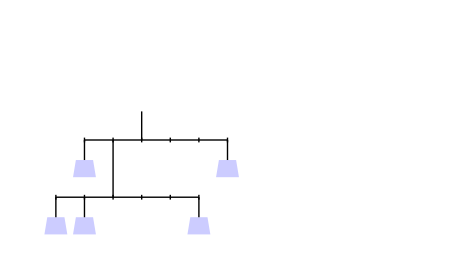

```mathematica
Style[Show[Graphics[{w[0,0,2],w[1,0,5],w[5,0,3],ll[0,0,5,1,2],w[1,2,1],w[6,2,4],l[1,2,5,1,3]
}],AspectRatio->Automatic,PlotRange->{{-0.5,12.5},{-2,6}},ImageSize->35{13,8}],Antialiasing->False]
```

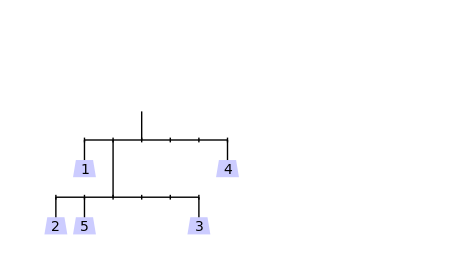

```mathematica
Style[Show[Graphics[{w[0,0,2],w[1,0,5],w[5,0,3],ll[0,0,5,1,2],w[1,2,1],w[6,2,4],l[1,2,5,1,3]
}],AspectRatio->Automatic,PlotRange->{{-0.5,12.5},{-2,6}},ImageSize->35{13,8}],Antialiasing->False]
```

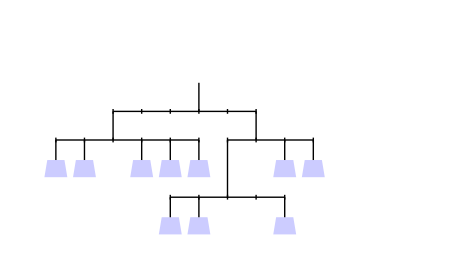

```mathematica
Style[Show[Graphics[{w[4,0,2],w[5,0,10],w[8,0,7],ll[4,0,4,1,6],w[8,2,9],w[9,2,5],l[6,2,3,1,7],w[0,2,3],w[1,2,3],w[3,2,4],w[4,2,6],w[5,2,1],l[0,2,5,1,2],l[2,3,5,1,5]
}],AspectRatio->Automatic,PlotRange->{{-0.5,12.5},{-2,6}},ImageSize->35{13,8}],Antialiasing->False]
```

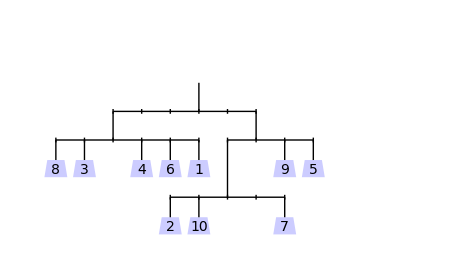

```mathematica
Style[Show[Graphics[{w[4,0,2],w[5,0,10],w[8,0,7],ll[4,0,4,1,6],w[8,2,9],w[9,2,5],l[6,2,3,1,7],w[0,2,8],w[1,2,3],w[3,2,4],w[4,2,6],w[5,2,1],l[0,2,5,1,2],l[2,3,5,1,5]
}],AspectRatio->Automatic,PlotRange->{{-0.5,12.5},{-2,6}},ImageSize->35{13,8}],Antialiasing->False]
```

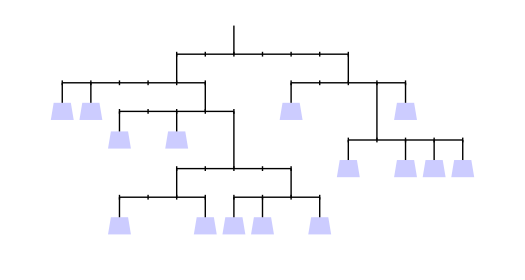

```mathematica
Style[Show[Graphics[{w[2,0,7],w[5,0,14],l[2,0,3,1,4],w[6,0,3],w[7,0,6],w[9,0,12],l[6,0,3,1,8],ll[4,1,4,1,6],w[2,3,11],w[4,3,9],l[2,3,4,1,5],w[0,4,8],w[1,4,10],l[0,4,5,1,4],l[4,5,6,1,6],l[8,4,4,1,10],w[8,4,15],w[12,4,5],ll[10,2,4,1,11],w[10,2,13],w[12,2,2],w[13,2,4],w[14,2,1]
}],AspectRatio->Automatic,PlotRange->{{-0.5,14.5},{-2,6}},ImageSize->35{15,8}],Antialiasing->False]
```

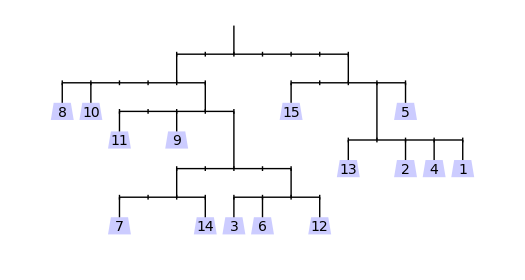

```mathematica
Style[Show[Graphics[{w[2,0,7],w[5,0,14],l[2,0,3,1,4],w[6,0,3],w[7,0,6],w[9,0,12],l[6,0,3,1,8],ll[4,1,4,1,6],w[2,3,11],w[4,3,9],l[2,3,4,1,5],w[0,4,8],w[1,4,10],l[0,4,5,1,4],l[4,5,6,1,6],l[8,4,4,1,10],w[8,4,15],w[12,4,5],ll[10,2,4,1,11],w[10,2,13],w[12,2,2],w[13,2,4],w[14,2,1]
}],AspectRatio->Automatic,PlotRange->{{-0.5,14.5},{-2,6}},ImageSize->35{15,8}],Antialiasing->False]
```

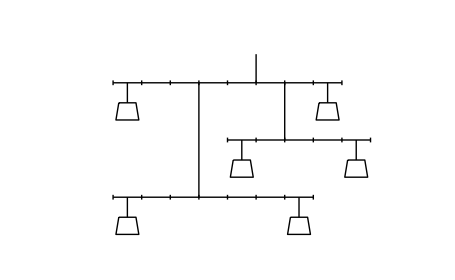

```mathematica
Show[Graphics[{w[2.5,0,4],w[8.5,0,3],ll[2,0,7,1,5],w[6.5,2,6],w[10.5,2,2],ll[6,2,5,1,8],w[9.5,4,5],w[2.5,4,1],l[2,4,8,1,7],Line[{{5,2},{5,4}}]}],AspectRatio->Automatic,PlotRange->{{-0.5,12.5},{-2,6}},ImageSize->35{13,8}]
```

```mathematica
{8,6,8,10}{2,4,1,3,9,6,9,11}
```

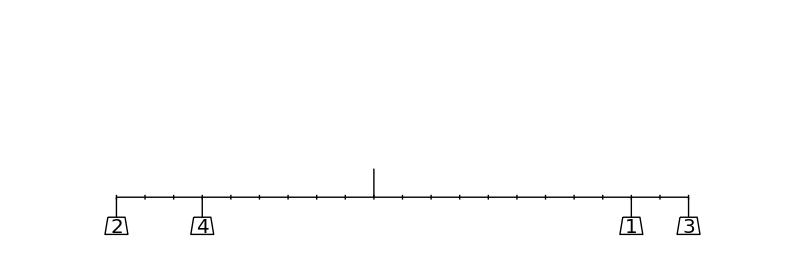

```mathematica
Show[Graphics[{w[-9,0,2],w[-6,0,4],w[9,0,1],w[11,0,3],l[-9,0,20,1,0]}],AspectRatio->Automatic,PlotRange->{{-10.5,12.5},{-2,6}},ImageSize->35{23,8}]
```

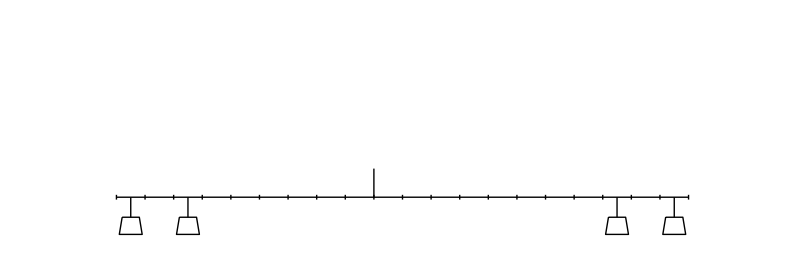

```mathematica
Show[Graphics[{w[-8.5,0,2],w[-6.5,0,4],w[8.5,0,1],w[10.5,0,3],l[-9,0,20,1,0]}],AspectRatio->Automatic,PlotRange->{{-10.5,12.5},{-2,6}},ImageSize->35{23,8}]
```

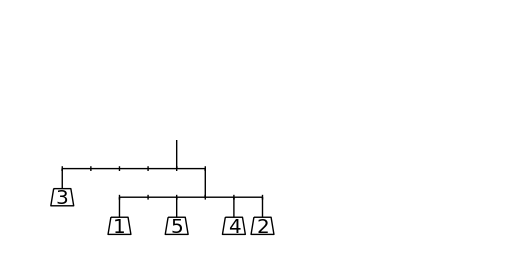

```mathematica
Style[Show[Graphics[{w[2,0,1],w[4,0,5],w[6,0,4],w[7,0,2],l[2,0,5,1,5],w[0,1,3],l[0,1,5,1,4]
}],AspectRatio->Automatic,PlotRange->{{-0.5,14.5},{-2,6}},ImageSize->35{15,8}],Antialiasing->False]
```

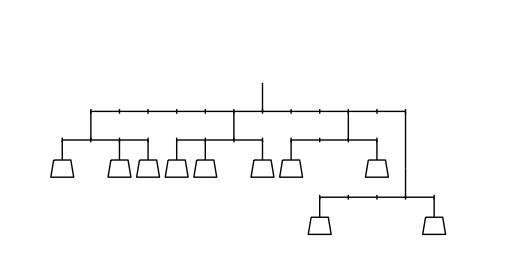

```mathematica
Style[Show[Graphics[{w[0,2,7],w[2,2,5],w[3,2,1],w[4,2,2],w[5,2,6],w[7,2,10],w[8,2,4],w[11,2,8],l[0,2,3,1,1],l[4,2,3,1,6],l[8,2,3,1,10],l[1,3,11,1,7],l[9,0,4,1,12],w[9,0,3],w[13,0,9],Line[{{12,1},{12,3}}]
}],AspectRatio->Automatic,PlotRange->{{-0.5,14.5},{-2,6}},ImageSize->35{15,8}],Antialiasing->False]
```

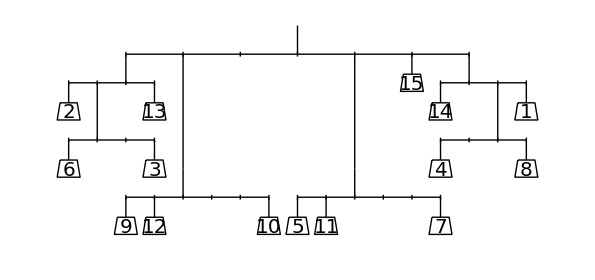

```mathematica
Style[Show[Graphics[{w[2,0,9],w[3,0,12],w[7,0,10],w[8,0,5],w[9,0,11],w[13,0,7],l[2,0,5,1,4],l[8,0,5,1,10],Line[{{4,1},{4,5}}],Line[{{10,1},{10,5}}],w[0,2,6],w[3,2,3],w[0,4,2],w[3,4,13],ll[0,2,3,1,1],l[0,4,3,1,2],w[13,2,4],w[16,2,8],w[13,4,14],w[16,4,1],ll[13,2,3,1,15],l[13,4,3,1,14],l[2,5,12,2,8],w[12,5,15]
}],AspectRatio->Automatic,PlotRange->{{-0.5,16.5},{-2,6}},ImageSize->35{17,8}],Antialiasing->False]
```

```mathematica
w[x_,y_,n_]:=Style[{Line[{{x,y},{x,y-.7}}],Line[{{x-.3,y-.7},{x+.3,y-.7},{x+.4,y-1.3},{x-.4,y-1.3},{x-.3,y-.7}}],Text[Style[n,FontFamily->"Courier", FontSize->20],{x,y-1.05}]},Antialiasing->False]
```

```mathematica
w[x_,y_,n_]:=Style[{Line[{{x,y},{x,y-.7}}],Line[{{x-.3,y-.7},{x+.3,y-.7},{x+.4,y-1.3},{x-.4,y-1.3},{x-.3,y-.7}}]},Antialiasing->False]
```

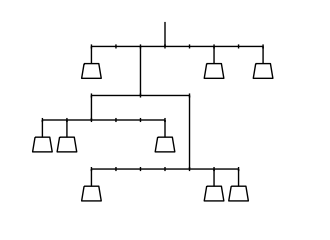

```mathematica
Style[Show[Graphics[{w[2,0,3],w[7,0,8],w[8,0,2],ll[2,0,6,1,6],w[0,2,7],w[1,2,1],w[5,2,5],l[0,2,5,1,2],w[2,5,6],w[7,5,4],w[9,5,9],l[2,5,7,1,5],ll[2,3,4,2,4],Line[{{6,2},{6,3}}]}],AspectRatio->Automatic,PlotRange->{{-0.5,10.5},{-2,6}},ImageSize->{330,240}],Antialiasing->False]
```

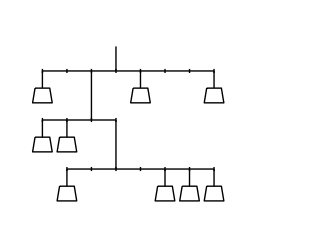

```mathematica
Style[Show[Graphics[{w[1,0,9],w[5,0,4],w[6,0,2],w[7,0,1],ll[1,0,6,1,3],w[0,2,5],w[1,2,6],ll[0,2,3,1,2],w[0,4,3],w[4,4,8],w[7,4,7],l[0,4,7,1,3]}],AspectRatio->Automatic,PlotRange->{{-0.5,10.5},{-2,6}},ImageSize->{330,240}],Antialiasing->False]
```

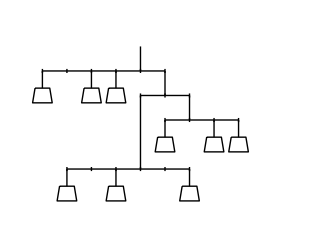

```mathematica
Style[Show[Graphics[{w[1,0,3],w[3,0,5],w[6,0,7],ll[1,0,5,1,4],w[5,2,8],w[7,2,6],w[8,2,1],l[5,2,3,1,6],l[4,3,2,1,5],Line[{{4,2},{4,3}}],w[0,4,2],w[2,4,9],w[3,4,4],l[0,4,5,1,4]}],AspectRatio->Automatic,PlotRange->{{-0.5,10.5},{-2,6}},ImageSize->{330,240}],Antialiasing->False]
```

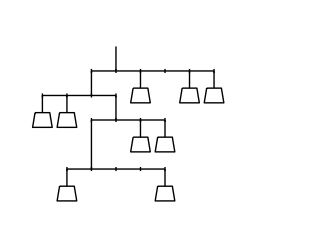

```mathematica
Style[Show[Graphics[{w[1,0,9],w[5,0,3],ll[1,0,4,1,2],w[4,2,2],w[5,2,5],l[2,2,3,1,3],w[0,3,6],w[1,3,7],l[0,3,3,1,2],w[4,4,4],w[6,4,8],w[7,4,1],l[2,4,5,1,3]}],AspectRatio->Automatic,PlotRange->{{-0.5,10.5},{-2,6}},ImageSize->{330,240}],Antialiasing->False]
```

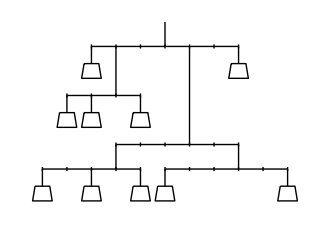

```mathematica
Style[Show[Graphics[{w[0,0,2],w[2,0,1],w[4,0,7],l[0,0,4,1,3],w[5,0,6],w[10,0,9],l[5,0,5,1,8],l[3,1,5,1,6],w[1,3,3],w[2,3,4],w[4,3,10],ll[1,3,3,1,3],w[2,5,5],w[8,5,8],l[2,5,6,1,5],Line[{{6,2},{6,5}}]}],AspectRatio->Automatic,PlotRange->{{-0.5,10.5},{-2,6}},ImageSize->{330,240}],Antialiasing->False]
```

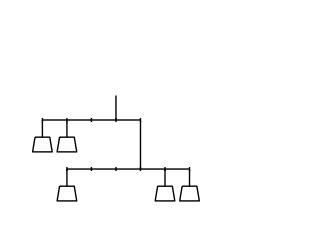

```mathematica
Style[Show[Graphics[{w[1,0,4],w[5,0,2],w[6,0,5],ll[1,0,5,1,4],l[0,2,4,1,3],w[0,2,3],w[1,2,1]}],AspectRatio->Automatic,PlotRange->{{-0.5,10.5},{-2,6}},ImageSize->{330,240}],Antialiasing->False]
```

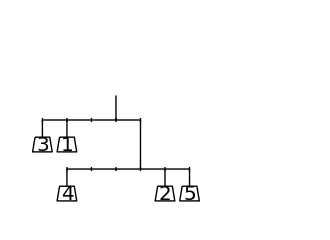

```mathematica
Style[Show[Graphics[{w[1,0,4],w[5,0,2],w[6,0,5],ll[1,0,5,1,4],l[0,2,4,1,3],w[0,2,3],w[1,2,1]}],AspectRatio->Automatic,PlotRange->{{-0.5,10.5},{-2,6}},ImageSize->{330,240}],Antialiasing->False]
```

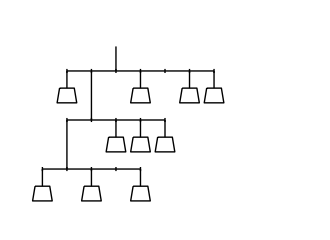

```mathematica
Style[Show[Graphics[{w[0,0,10],w[2,0,7],w[4,0,1],ll[0,0,4,1,1],w[3,2,5],w[4,2,2],w[5,2,3],ll[1,2,4,1,2],w[1,4,9],w[4,4,6],w[6,4,8],w[7,4,4],l[1,4,6,1,3]}],AspectRatio->Automatic,PlotRange->{{-0.5,10.5},{-2,6}},ImageSize->{330,240}],Antialiasing->False]
```

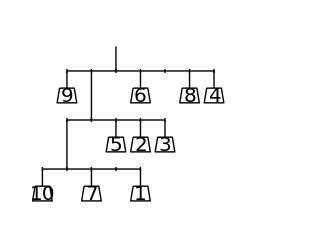

```mathematica
Style[Show[Graphics[{w[0,0,10],w[2,0,7],w[4,0,1],ll[0,0,4,1,1],w[3,2,5],w[4,2,2],w[5,2,3],ll[1,2,4,1,2],w[1,4,9],w[4,4,6],w[6,4,8],w[7,4,4],l[1,4,6,1,3]}],AspectRatio->Automatic,PlotRange->{{-0.5,10.5},{-2,6}},ImageSize->{330,240}],Antialiasing->False]
```

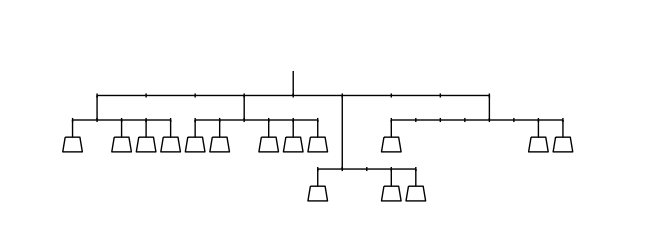

```mathematica
Style[Show[Graphics[{w[10,0,14],w[13,0,4],w[14,0,2],ll[10,0,4,1,11],Line[{{11,3},{11,2}}],w[0,2,15],w[2,2,6],w[3,2,3],w[4,2,1],l[0,2,4,1,1],w[5,2,13],w[6,2,11],w[8,2,8],w[9,2,7],w[10,2,5],l[5,2,5,1,7],l[1,3,16,2,9],w[13,2,12],w[19,2,9],w[20,2,10],l[13,2,7,1,17]}],AspectRatio->Automatic,PlotRange->{{-0.5,21.5},{-2,6}},ImageSize->{660,240}],Antialiasing->False]
```

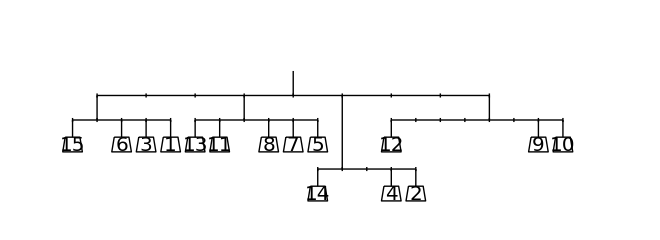

```mathematica
Style[Show[Graphics[{w[10,0,14],w[13,0,4],w[14,0,2],ll[10,0,4,1,11],Line[{{11,3},{11,2}}],w[0,2,15],w[2,2,6],w[3,2,3],w[4,2,1],l[0,2,4,1,1],w[5,2,13],w[6,2,11],w[8,2,8],w[9,2,7],w[10,2,5],l[5,2,5,1,7],l[1,3,16,2,9],w[13,2,12],w[19,2,9],w[20,2,10],l[13,2,7,1,17]}],AspectRatio->Automatic,PlotRange->{{-0.5,21.5},{-2,6}},ImageSize->{660,240}],Antialiasing->False]
```

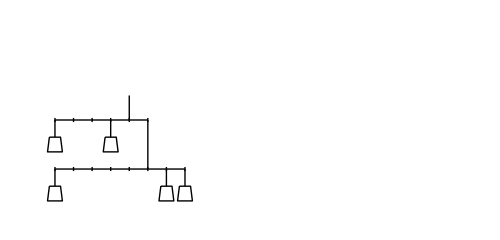

```mathematica
Style[Show[Graphics[{w[0,0,2],w[6,0,4],w[7,0,3],ll[0,0,7,1,5],w[0,2,1],w[3,2,5],l[0,2,5,1,4]}],AspectRatio->Automatic,PlotRange->{{-0.5,21.5},{-2,6}},ImageSize->{500,240}],Antialiasing->False]
```

```mathematica
w[x_,y_,n_]:=Style[{Line[{{x-.3,1.3+y-.7},{x+.3,1.3+y-.7},{x+.4,1.3+y-1.3},{x-.4,1.3+y-1.3},{x-.3,1.3+y-.7}}],Text[Style[n,FontFamily->"Courier", FontSize->18],{x,1.3+y-1.05}]},Antialiasing->False]
```

```mathematica
w[x_,y_,n_]:=Style[{Line[{{x-.3,1.3+y-.7},{x+.3,1.3+y-.7},{x+.4,1.3+y-1.3},{x-.4,1.3+y-1.3},{x-.3,1.3+y-.7}}]},Antialiasing->False]
```

```mathematica
l[x_,y_,n_,m_,p_,h_]:=Style[{Line[{{x,y},{x+n,y}}],Table[Line[{{a,y},{a,y-1/12}}],{a,x,x+n,m}],Line[{{p,y},{p,y+h}}]},Antialiasing->False]
```

```mathematica
ll[x_,y_,n_,m_,p_]:=Style[{Line[{{x,y},{x+n,y}}],Table[Line[{{a,y},{a,y-1/12}}],{a,x,x+n,m}],Line[{{p,y},{p,y+2}}]},Antialiasing->False]
```

```mathematica
lll[x_,y_,n_,m_,p_]:=Style[{Line[{{x,y},{x+n,y}}],Table[Line[{{a,y},{a,y-1/12}}],{a,x,x+n,m}],Line[{{p,y},{p,y+3}}]},Antialiasing->False]
```

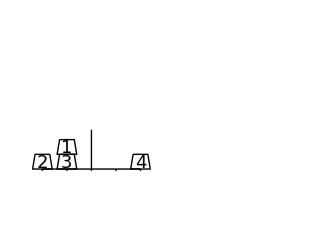

```mathematica
Show[Graphics[{w[0,0,2],w[1,0,3],w[1,.6,1],w[4,0,4],l[0,0,4,1,2,1.6]}],AspectRatio->Automatic,PlotRange->{{-0.5,10.5},{-2,6}},ImageSize->{330,240}]
```

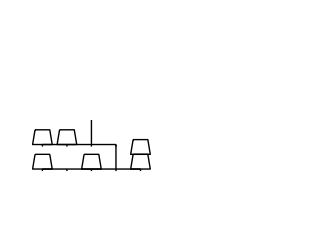

```mathematica
Show[Graphics[{w[0,0,1],w[2,0,4],w[4,0,5],w[4,.6,2],l[0,0,4,1,3,1],w[0,1,3],w[1,1,6],l[0,1,3,1,2,1]}],AspectRatio->Automatic,PlotRange->{{-0.5,10.5},{-2,6}},ImageSize->{330,240}]
```

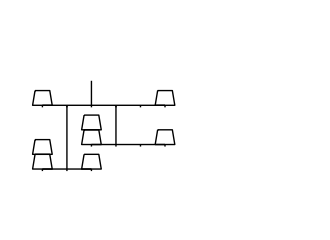

```mathematica
Show[Graphics[{w[0,0,3],w[0,.6,1],w[2,0,4],l[0,0,2,1,1,2.6],w[2,1,7],w[2,1.6,5],w[5,1,6],l[2,1,3,1,3,1.6],w[0,2.6,8],w[5,2.6,2],l[0,2.6,5,1,2,1]}],AspectRatio->Automatic,PlotRange->{{-0.5,10.5},{-2,6}},ImageSize->{330,240}]
```

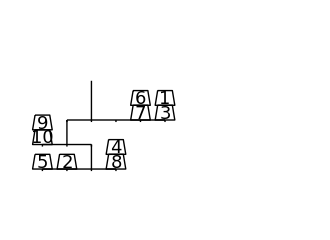

```mathematica
Show[Graphics[{w[0,0,5],w[1,0,2],w[3,0,8],w[3,.6,4],l[0,0,3,1,2,1],w[0,1,10],w[0,1.6,9],l[0,1,2,1,1,1],w[4,2,7],w[4,2.6,6],w[5,2,3],w[5,2.6,1],l[1,2,4,1,2,1.6]}],AspectRatio->Automatic,PlotRange->{{-0.5,10.5},{-2,6}},ImageSize->{330,240}]
```

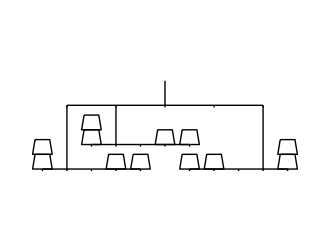

```mathematica
Show[Graphics[{w[0,0,7],w[0,.6,6],w[3,0,2],w[4,0,3],l[0,0,4,1,1,2.6],w[6,0,5],w[7,0,4],w[10,0,12],w[10,.6,11],l[6,0,4,1,9,2.6],w[2,1,10],w[2,1.6,9],w[5,1,8],w[6,1,1],l[2,1,4,1,3,1.6],l[1,2.6,8,2,5,1]}],AspectRatio->Automatic,PlotRange->{{-0.5,10.5},{-2,6}},ImageSize->{330,240}]
```

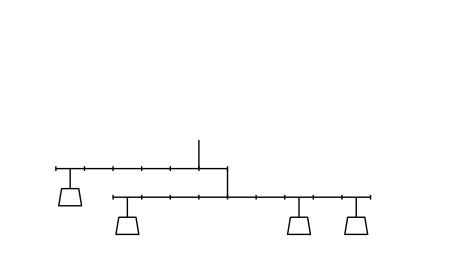

```mathematica
Show[Graphics[{w[2.5,0,3],w[8.5,0,4],w[10.5,0,1],l[2,0,9,1,6],w[0.5,1,2],l[0,1,6,1,5]}],AspectRatio->Automatic,PlotRange->{{-0.5,12.5},{-2,6}},ImageSize->35{13,8}]
```

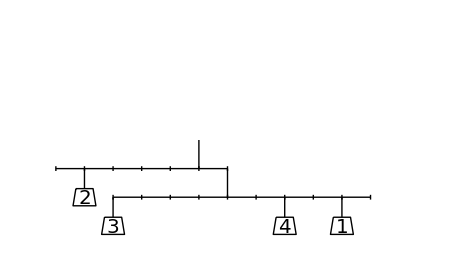

```mathematica
Show[Graphics[{w[2,0,3],w[8,0,4],w[10,0,1],l[2,0,9,1,6],w[1,1,2],l[0,1,6,1,5]}],AspectRatio->Automatic,PlotRange->{{-0.5,12.5},{-2,6}},ImageSize->35{13,8}]
```

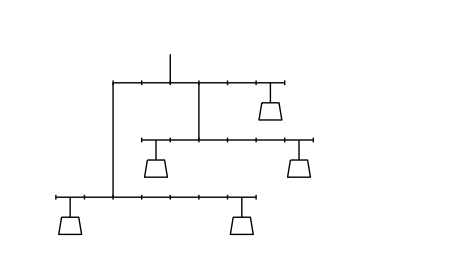

```mathematica
Show[Graphics[{w[.5,0,5],w[6.5,0,2],lll[0,0,7,1,2],w[3.5,2,4],w[8.5,2,1],ll[3,2,6,1,5],l[2,4,6,1,4],w[7.5,4,3]}],AspectRatio->Automatic,PlotRange->{{-0.5,12.5},{-2,6}},ImageSize->35{13,8}]
```

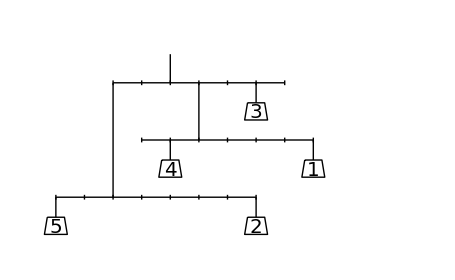

```mathematica
Show[Graphics[{w[0,0,5],w[7,0,2],lll[0,0,7,1,2],w[4,2,4],w[9,2,1],ll[3,2,6,1,5],l[2,4,6,1,4],w[7,4,3]}],AspectRatio->Automatic,PlotRange->{{-0.5,12.5},{-2,6}},ImageSize->35{13,8}]
```

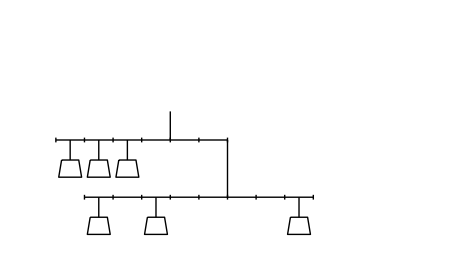

```mathematica
Show[Graphics[{w[1.5,0,2],w[3.5,0,5],w[8.5,0,6],ll[1,0,8,1,6],l[0,2,6,1,4],w[.5,2,1],w[1.5,2,3],w[2.5,2,4]}],AspectRatio->Automatic,PlotRange->{{-0.5,12.5},{-2,6}},ImageSize->35{13,8}]
```

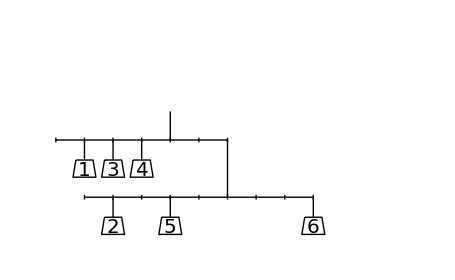

```mathematica
Show[Graphics[{w[2,0,2],w[4,0,5],w[9,0,6],ll[1,0,8,1,6],l[0,2,6,1,4],w[1,2,1],w[2,2,3],w[3,2,4]}],AspectRatio->Automatic,PlotRange->{{-0.5,12.5},{-2,6}},ImageSize->35{13,8}]
```

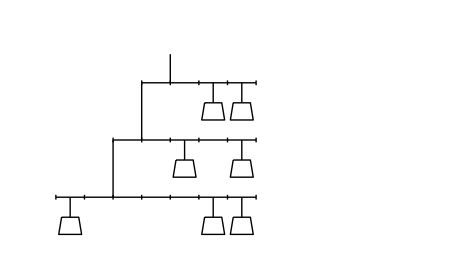

```mathematica
Show[Graphics[{w[.5,0,7],w[5.5,0,3],w[6.5,0,1],ll[0,0,7,1,2],ll[2,2,5,1,3],w[4.5,2,5],w[6.5,2,2],l[3,4,4,1,4],w[5.5,4,6],w[6.5,4,4]}],AspectRatio->Automatic,PlotRange->{{-0.5,12.5},{-2,6}},ImageSize->35{13,8}]
```

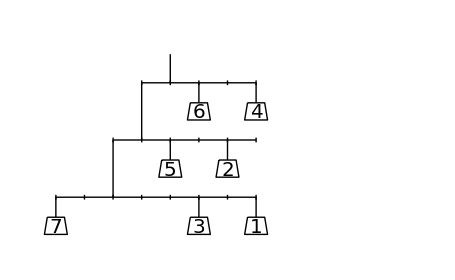

```mathematica
Show[Graphics[{w[0,0,7],w[5,0,3],w[7,0,1],ll[0,0,7,1,2],ll[2,2,5,1,3],w[4,2,5],w[6,2,2],l[3,4,4,1,4],w[5,4,6],w[7,4,4]}],AspectRatio->Automatic,PlotRange->{{-0.5,12.5},{-2,6}},ImageSize->35{13,8}]
```

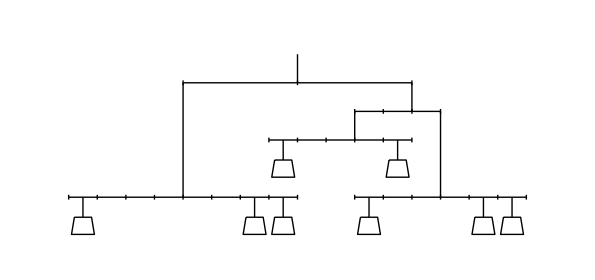

```mathematica
Show[Graphics[{w[.5,0,7],w[6.5,0,8],w[7.5,0,3],lll[0,0,8,1,4],l[7,2,5,1,10],w[7.5,2,2],w[11.5,2,4],ll[10,0,6,1,13],w[10.5,0,5],w[14.5,0,6],w[15.5,0,1],l[4,4,8,4,8],l[10,3,3,1,12],Style[Line[{{13,2},{13,3}}],Antialiasing->False]}],AspectRatio->Automatic,PlotRange->{{-0.5,16.5},{-2,6}},ImageSize->35{17,8}]
```

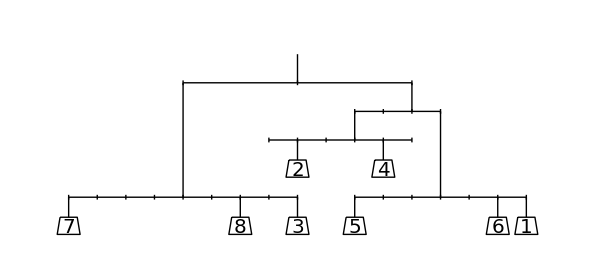

```mathematica
Show[Graphics[{w[0,0,7],w[6,0,8],w[8,0,3],lll[0,0,8,1,4],l[7,2,5,1,10],w[8,2,2],w[11,2,4],ll[10,0,6,1,13],w[10,0,5],w[15,0,6],w[16,0,1],l[4,4,8,4,8],l[10,3,3,1,12],Style[Line[{{13,2},{13,3}}],Antialiasing->False]}],AspectRatio->Automatic,PlotRange->{{-0.5,16.5},{-2,6}},ImageSize->35{17,8}]
```

```mathematica
w[x_,y_,n_]:=Style[{Line[{{x,y},{x,y-.7}}],Line[{{x-.3,y-.7},{x+.3,y-.7},{x+.4,y-1.3},{x-.4,y-1.3},{x-.3,y-.7}}],Text[Style[n,FontFamily->"Courier", FontSize->20],{x,y-1.02}]},Antialiasing->False]
```

```mathematica
ww[x_,y_,n_]:=Style[{Line[{{x,y-.3},{x,y-.7}}],Line[{{x-.3,y-.7},{x+.3,y-.7},{x+.4,y-1.3},{x-.4,y-1.3},{x-.3,y-.7}}],Text[Style[n,FontFamily->"Courier", FontSize->20],{x,y-1.02}]},Antialiasing->False]
```

```mathematica
w[x_,y_,n_]:=Style[{Line[{{x,y},{x,y-.7}}],Line[{{x-.3,y-.7},{x+.3,y-.7},{x+.4,y-1.3},{x-.4,y-1.3},{x-.3,y-.7}}]},Antialiasing->False]
```

```mathematica
ww[x_,y_,n_]:=Style[{Line[{{x,y-.3},{x,y-.7}}],Line[{{x-.3,y-.7},{x+.3,y-.7},{x+.4,y-1.3},{x-.4,y-1.3},{x-.3,y-.7}}]},Antialiasing->False]
```

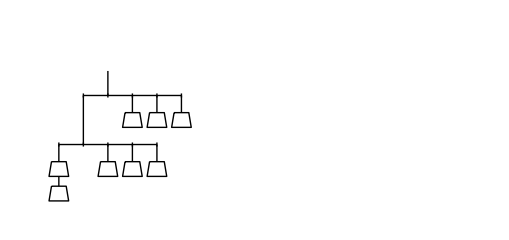

```mathematica
Style[Graphics[{ww[0,0,4],w[0,1,4],w[2,1,3],w[3,1,1],w[4,1,1],ll[0,1,4,1,1],l[1,3,4,1,2],w[3,3,3],w[4,3,2],w[5,3,2]},AspectRatio->Automatic,PlotRange->{{-0.5,16.5},{-2,6}},ImageSize->30{17,8}],Antialiasing->False]
```

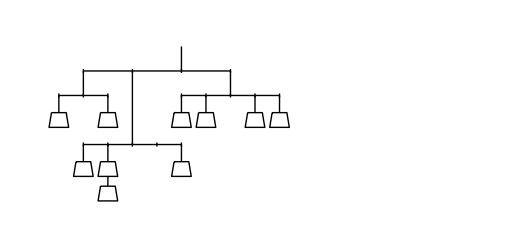

```mathematica
Style[Graphics[{ww[2,0,1],w[2,1,1],w[1,1,3],w[5,1,4],lll[1,1,4,1,3],w[0,3,2],w[2,3,2],l[0,3,2,1,1],w[5,3,4],w[6,3,5],w[8,3,3],w[9,3,5],l[5,3,4,1,7],l[1,4,6,2,5]},AspectRatio->Automatic,PlotRange->{{-0.5,16.5},{-2,6}},ImageSize->30{17,8}],Antialiasing->False]
```

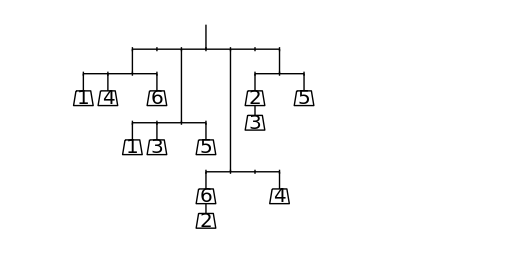

```mathematica
Style[Graphics[{ww[6,0,2],w[6,1,6],w[9,1,4],lll[6,1,3,1,7],w[6,3,5],w[4,3,3],w[3,3,1],ll[3,3,3,1,5],w[4,5,6],w[2,5,4],w[1,5,1],l[1,5,3,1,3],ww[8,4,3],w[8,5,2],w[10,5,5],l[8,5,2,1,9],l[3,6,6,1,6]},AspectRatio->Automatic,PlotRange->{{-0.5,16.5},{-2,7}},ImageSize->30{17,9}],Antialiasing->False]
```

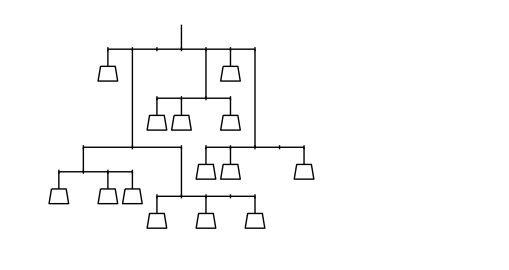

```mathematica
Style[Graphics[{w[0,1,6],w[2,1,4],w[3,1,1],l[0,1,3,1,1],w[4,0,7],w[6,0,1],w[8,0,3],ll[4,0,4,1,5],lll[1,2,4,2,3],w[6,2,5],w[7,2,2],w[10,2,6],lll[6,2,4,1,8],w[4,4,2],w[5,4,3],w[7,4,7],ll[4,4,3,1,6],w[2,6,5],w[7,6,4],l[2,6,6,1,5]},AspectRatio->Automatic,PlotRange->{{-0.5,16.5},{-2,7}},ImageSize->30{17,9}],Antialiasing->False]
```

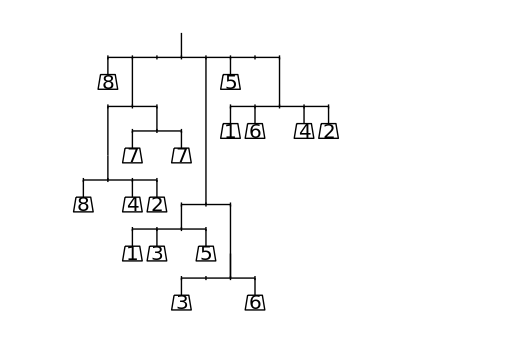

```mathematica
Style[Graphics[{l[2,6,7,1,5],w[2,6,8],w[7,6,5],ll[7,4,4,1,9],w[7,4,1],w[8,4,6],w[10,4,4],w[11,4,2],l[5,0,2,1,6],l[3,-1,3,1,5],w[3,-1,1],w[4,-1,3],w[6,-1,5],l[5,-3,3,1,7],w[5,-3,3],w[8,-3,6],ll[2,4,2,1,3],l[3,3,2,1,4],w[3,3,7],w[5,3,7],l[1,1,3,1,2],w[1,1,8],w[3,1,4],w[4,1,2],Line[{{2,2},{2,4}}],Line[{{7,-3},{7,0}}],Line[{{6,1},{6,6}}]},AspectRatio->Automatic,PlotRange->{{-0.5,16.5},{-5,7}},ImageSize->30{17,12}],Antialiasing->False]
```

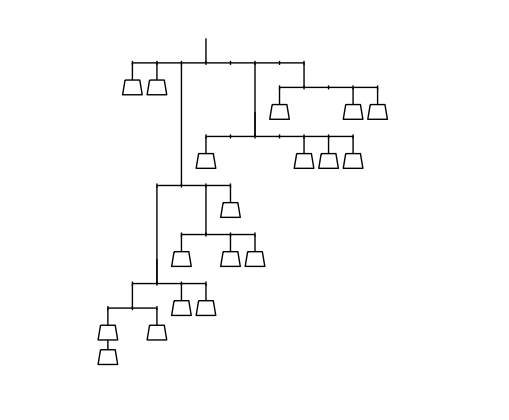

```mathematica
Style[Graphics[{l[3,6,7,1,6],w[3,6,5],w[4,6,7],l[9,5,4,1,10],w[9,5,9],w[12,5,3],w[13,5,1],l[6,3,6,1,8],w[6,3,8],w[10,3,3],w[11,3,2],w[12,3,1],Line[{{8,3},{8,6}}],Line[{{5,6},{5,2}}],l[4,1,3,1,5],w[7,1,7],ll[5,-1,3,1,6],w[5,-1,8],w[7,-1,4],w[8,-1,2],l[3,-3,3,1,4],w[5,-3,6],w[6,-3,6],Line[{{4,-3},{4,1}}],l[2,-4,2,1,3],w[4,-4,9],w[2,-4,5],ww[2,-5,4]
},AspectRatio->Automatic,PlotRange->{{-0.5,16.5},{-7,7}},ImageSize->30{17,14}],Antialiasing->False]
```